```mathematica
filename="averages_n_checksfrom4to9second_test_prec=88seed=3.txt";
data=Get[filename];
```

```mathematica
dims=data[[1,Range[1,11,2]]];
opes=data[[1,Range[2,12,2]]];
```

```mathematica
dims//Dimensions
```

{6,2}

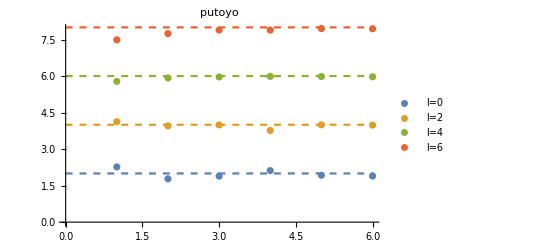

```mathematica
a=ListPlot[dims[[;;,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"}];
ref=Plot[{2,4,6,8},{x,0,6},PlotStyle->Dashed];
Show[a,ref,PlotLabel->"putoyo"]
```

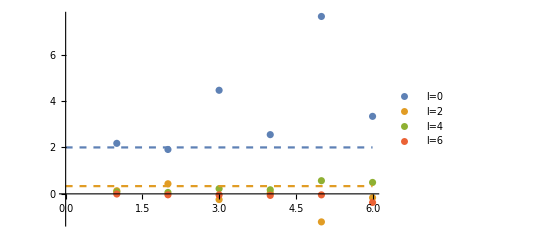

```mathematica
mc=ListPlot[opes[[;;,1,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"}];
ref=Plot[{2,1/3},{x,0,6},PlotStyle->Dashed];
Show[mc,ref]
```

```mathematica
opes[[;;,2]]
```

{True,True,True,True,True,True}

```mathematica
mcPlotDimsAndOPEs[initialOps_,finalOps_,nz_,prec_,seed_,runid_]:=Block[{data,dims,opes,mcDims,mcOpes,refDims,refOpes,nrecs=(finalOps-initialOps) +1},
data= Get["averages_n_checks"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>".txt"];
dims=data[[1,Range[1,2nrecs -1,2]]];
opes=data[[1,Range[2,2nrecs ,2]]];
mcDims=ListPlot[dims[[;;,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"}];
refDims=Plot[{2,4,6,8},{x,0,nrecs},PlotStyle->Dashed];
mcOpes=ListPlot[opes[[;;,1,1,1;;4]]//Transpose,PlotLegends->{"l=0","l=2","l=4","l=6"}];
refOpes=Plot[{2,1/3},{x,0,nrecs},PlotStyle->Dashed];
Export["dims-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>".pdf",Show[mcDims,refDims],PlotLabel->"Dims_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Export["opes-plot"<>"from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]<>".pdf",Show[mcOpes,refOpes],PlotLabel->"OPEs_from"<>ToString[initialOps]<>"to"<>ToString[finalOps]<>runid<>"prec="<>ToString[prec]<>"seed="<>ToString[seed]];
Return[opes[[;;,2]]]]
```

```mathematica
βvec={1/7,1/9,1/10,1/11,1/12,1/13};
nvec={3000,2000,2000,2000,2000,2000};
ΔLinitial={#+1,#-2}&/@Range[2,18,2];
mcPlotDimsAndOPEs[4,9,1000,88,2,"second_test_"]
```

{False,True,False,False,False,False}